```mathematica
(** This is code modified specifically for the 2d case **)
(** Set the directory that you want your plots to go to here **)
SetDirectory["/users/maxzweig/energythrust"]
```

/Users/maxzweig/energythrust

```mathematica
(** Various helper functions for standard parts of the paper / reachable set results **)
CW[n_] := {{0, 0, 0,1, 0, 0}, {0, 0, 0,0,1, 0}, {0, 0, 0, 0 ,0, 1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0, 0}, {0, 0, -n^2, 0, 0,0}} ;
xrf[tf_, delta_, h_, deltaT_, n_, Rr_, emax_] := NIntegrate[  emax ({{-Sin[n (tau-tf)]/n,(2 (-1+Cos[n (tau-tf)]))/n,0},{-(2 (-1+Cos[n (tau-tf)]))/n,3 tau-3 tf-(4 Sin[n (tau-tf)])/n,0},{0,0,-Sin[n (tau-tf)]/n}} // Transpose).{{-Sin[n (tau-tf)]/n,(2 (-1+Cos[n (tau-tf)]))/n,0},{-(2 (-1+Cos[n (tau-tf)]))/n,3 tau-3 tf-(4 Sin[n (tau-tf)])/n,0},{0,0,-Sin[n (tau-tf)]/n}}.delta / (deltaT.({{-Sin[n (tau-tf)]/n,(2 (-1+Cos[n (tau-tf)]))/n,0},{-(2 (-1+Cos[n (tau-tf)]))/n,3 tau-3 tf-(4 Sin[n (tau-tf)])/n,0},{0,0,-Sin[n (tau-tf)]/n}} // Transpose).{{-Sin[n (tau-tf)]/n,(2 (-1+Cos[n (tau-tf)]))/n,0},{-(2 (-1+Cos[n (tau-tf)]))/n,3 tau-3 tf-(4 Sin[n (tau-tf)])/n,0},{0,0,-Sin[n (tau-tf)]/n}}.delta // Sqrt)[[1]]  ,{tau, 0, tf}];
```

```mathematica
(** Computes the thrust-limited reachable set for a given final time **)
thrustreachable[xrf_,tf_, na_, emax_,numpoints_] := Module[{points, tfs, hs, As, ns, Rrs, pointsT, rd, rdpoints, rdboundary, first2},
points = CirclePoints[numpoints];
points = Append[#, 0] & /@ points;
points //  N;
points[[1]];
tfs = ConstantArray[tf, numpoints];
tfs[[1]];
hs = ConstantArray[1, numpoints];
hs[[1]];
ns = ConstantArray[na, numpoints];
ns[[1]];
Rrs = ConstantArray[1, numpoints];
Rrs[[1]];
emaxs = ConstantArray[emax, numpoints];
columntorow[x_] := {x};
pointsT = columntorow /@ points;
pointsT[[1]] // MatrixForm;

rd = MapThread[xrf, {tfs, points, hs, pointsT, ns, Rrs, emaxs}];
rdpoints = Map[Re, rd, {2}];
(* first2[x_] := {x[[1]], x[[2]]}; *)
(* rboundary = Map[first2, rdboundary];*)
rdpoints
]
```

```mathematica
(** Computes the energy reachable quadratic form for an associated n and final time **)
energyform[tff_, na_] := Module[{c, r, sig, gamma, nmat},
c[n_] = {
{0, -2* n, 0, 1, 0, 0},
{2 * n, 0, 0, 0, 1, 0},
{0, 0, 0, 0,0 , 1},
{-1, 0, 0, 0, 0, 0},
{0, -1, 0, 0,0,0 }, 
{0, 0, -1, 0, 0, 0 }
}; (*Good*)
c[n] // MatrixForm;
r[t_, h_] = {{72 t Cos[h t]+(154 h t+48 h^3 t^3-384 Sin[h t]-27 Sin[2 h t])/(4 h),-3 h t^2+(6-6 Cos[h t])/h,0,(8+12 h^2 t^2-8 Cos[h t]-24 h t Sin[h t]+9 Sin[h t]^2)/(2 h^2),(23 h t+6 h^3 t^3+42 h t Cos[h t]-56 Sin[h t]-9/2 Sin[2 h t])/h^2,0},{-3 h t^2+(6-6 Cos[h t])/h,t,0,(2 (-h t+Sin[h t]))/h^2,-(3 t^2)/2+(4-4 Cos[h t])/h^2,0},{0,0,(2 h t+Sin[2 h t])/(4 h),0,0,Sin[h t]^2/(2 h^2)},{(8+12 h^2 t^2-8 Cos[h t]-24 h t Sin[h t]+9 Sin[h t]^2)/(2 h^2),(2 (-h t+Sin[h t]))/h^2,0,(26 h t-32 Sin[h t]+3 Sin[2 h t])/(4 h^3),(3 (-h t+Sin[h t])^2)/h^3,0},{(23 h t+6 h^3 t^3+42 h t Cos[h t]-56 Sin[h t]-9/2 Sin[2 h t])/h^2,-(3 t^2)/2+(4-4 Cos[h t])/h^2,0,(3 (-h t+Sin[h t])^2)/h^3,(14 h t+3 h^3 t^3+24 h t Cos[h t]-32 Sin[h t]-3 Sin[2 h t])/h^3,0},{0,0,Sin[h t]^2/(2 h^2),0,0,-(-2 h t+Sin[2 h t])/(4 h^3)}};(*Good*)
r[t, n] // MatrixForm;
sig[t_, n_] = {{4-3 Cos[n t],0,0,Sin[n t]/n,(2-2 Cos[n t])/n,0},{6 (-n t+Sin[n t]),1,0,(2 (-1+Cos[n t]))/n,-3 t+(4 Sin[n t])/n,0},{0,0,Cos[n t],0,0,Sin[n t]/n},{3 n Sin[n t],0,0,Cos[n t],2 Sin[n t],0},{6 n (-1+Cos[n t]),0,0,-2 Sin[n t],-3+4 Cos[n t],0},{0,0,-n Sin[n t],0,0,Cos[n t]}}; (* Good *)
gamma[t_, t0_, n_] = sig[t, n]. (sig[t0, n] // Inverse);

nmat[t0_, tf_, n_] = (Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2] // Transpose). (c[n] // Transpose). (r[tf, n] // Inverse).c[n].Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2];
nmat[0, tff, na]
]
```

```mathematica
reachablestatsoperator[points_,axis1_,axis2_] := Module[{rats, vecs}, 
ellipseVecFromUnitVec[uv_,ax1_, ax2_]:=1/Sqrt[(Normalize[ax1].uv)^2/Norm[ax1]^2+(Normalize[ax2].uv)^2/Norm[ax2]^2]*uv;


ratio[pos_]:= Norm[ellipseVecFromUnitVec[Normalize[pos[[1;;2]]],axis1, axis2] ]/ Norm[pos[[1;;2]]];
maxminrat[ v1s_] := {(ratio/@v1s)// Max, (ratio/@v1s)// Min};
toq2q1[vec_] := If[(vec[[1]] < 0 && vec[[2]] < 0) || (vec[[1]] >0 && vec[[2]] < 0), -vec, vec];
maxminvec[ v1s_] := {v1s[[ Position[(ratio/@v1s), (ratio/@v1s) // Max    ][[1,1]]]] // toq2q1 , v1s[[ Position[(ratio/@v1s), (ratio/@v1s) // Min   ][[1,1]]]] // toq2q1};
rats = maxminrat[ points];
vecs = maxminvec[ points];
{rats , {vecs[[1, 1;;2]], vecs[[2, 1;;2]]}}
]
```

```mathematica
(** Sample parameter values **)
mu1 = 3.986 10^14 ;
endtime = 1500;
alpha = 7780000;
n = (mu1 / alpha^3)^(1/2);
n
tmax=2/1000;
comparableenergy = endtime tmax^2;

2Pi/n
```

0.000920024

6829.37

```mathematica
(** test of comparison statistics **)
testbounds = thrustreachable[xrf, endtime, n, tmax,numsamples];
testbounds[[1]]

(**teststats = reachablestatsoperator[ energyform[1600, n],testbounds, comparableenergy]**)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{1660.59,-2186.55,0.}

```mathematica
(** Threading the different terminal times through our energy and thrust limited RRS computations, and then through the ratio computations **) 
numsamples=10;
starts // Clear;
finaltime // Clear;
starts = 60; 
finaltime = 6829;
terminaltimes = Range[starts, finaltime, 60];
ns = ConstantArray[n, terminaltimes // Length];
tmaxs = ConstantArray[tmax, terminaltimes // Length];
xrfs = ConstantArray[xrf, terminaltimes // Length];
numpoints=ConstantArray[numsamples,terminaltimes // Length]
bounds = MapThread[thrustreachable, {xrfs, terminaltimes, ns, tmaxs,numpoints}];
forms = MapThread[energyform, {terminaltimes, ns}];
comparableenergies = terminaltimes tmax^2;
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
getAxes[terminaltime_, quadform_, thrustmax_] := Module[{testbounds, teststats},
energysetaxes[quad_] :=
Eigenvectors[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
energyseteigenvalues[quad_] :=  Eigenvalues[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
vecs = energysetaxes[quadform];
vals = energyseteigenvalues[quadform];
ax1 = vecs[[1]][[1;;2]] * ((terminaltime thrustmax^2* vals[[1]]) // Sqrt);
ax2 = vecs[[2]][[1;;2]] * ((terminaltime thrustmax^2* vals[[2]]) // Sqrt);
{ax1,ax2}]

getAxes[3600, energyform[3600, n], tmax]
```

{{18504.7,-38556.2},{-9241.21,-4435.25}}

```mathematica
(**Computing the commparisons **)
ellipseAxes=MapThread[getAxes, {terminaltimes,forms, tmaxs} ];
computedmmratios = MapThread[reachablestatsoperator, {bounds, ellipseAxes[[;;,1]],ellipseAxes[[;;,2]]} ];
maxrats = computedmmratios[[;;, 1, 1]];
minrats = computedmmratios[[;;, 1, 2]];
maxvecs = computedmmratios[[;;, 2, 1]];
minvecs = computedmmratios[[;;, 2, 2]];
vectoangle[k_] :=ArcTan[k[[1]],k[[2]]];
reflection[th_] := ArcTan[1 / (th // Tan)];
toq1q2[th_]:= If[th < 0, Pi + th, th];
maxangles = Map[vectoangle, maxvecs];
minangles = Map[vectoangle, minvecs];

maxangles = Map[reflection, maxangles];
minangles = Map[reflection, minangles];

maxangles = Map[toq1q2, maxangles];
minangles = Map[toq1q2, minangles];
```

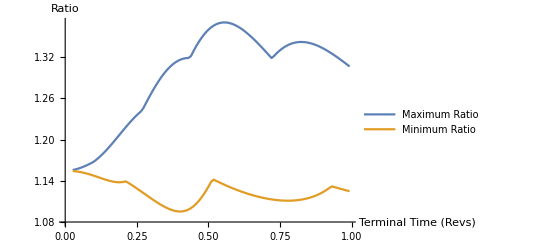

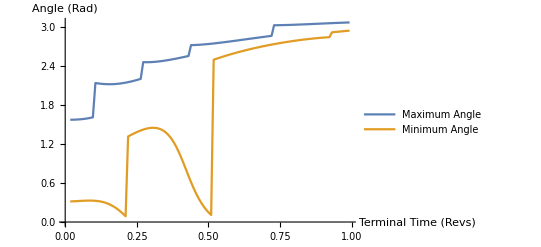

maxratt.png

minratt.png

maxanglet.png

minanglet.png

```mathematica
(** Plotting code **)
l1 = ListLinePlot[{{terminaltimes[[3;;]] / (2 Pi / n), maxrats[[3;;]]} // Transpose,{terminaltimes[[3;;]] / (2 Pi / n), minrats[[3;;]]} // Transpose}, AxesLabel-> {"Terminal Time (Revs)", "Ratio" } , PlotLegends->LineLegend[{"Maximum Ratio","Minimum Ratio"}]]  
(**l2 = ListLinePlot[{terminaltimes[[3;;]], minrats[[3;;]]} // Transpose, AxesLabel-> {"Terminal Time (s)", "Ratio" }] **)
l3 = ListLinePlot[{{terminaltimes[[2;;]] / (2 Pi / n), maxangles[[2;;]]} // Transpose,{terminaltimes[[2;;]] / (2 Pi / n), minangles[[2;;]]} // Transpose}, AxesLabel-> {"Terminal Time (Revs)", "Angle (Rad)" }, PlotLegends->LineLegend[{"Maximum Angle","Minimum Angle"}]]
(**l4 = ListLinePlot[{terminaltimes[[2;;]], minangles[[2;;]]} // Transpose, AxesLabel-> {"Terminal Time (s)", "Angle (Rad)"}] **)

Export["maxratt.png", l1]
Export["minratt.png", l2]
Export["maxanglet.png", l3]
Export["minanglet.png", l4]
```

```mathematica
endtime // Clear;
plotrrs[terminaltime_, quadform_, thrustmax_, n_] := Module[{testbounds, teststats},
energysetaxes[quad_] :=
Eigenvectors[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
energyseteigenvalues[quad_] :=  Eigenvalues[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
vecs = energysetaxes[quadform];
vals = energyseteigenvalues[quadform];
ax1 = vecs[[1]][[1;;2]] * ((terminaltime thrustmax^2* vals[[1]]) // Sqrt);
ax2 = vecs[[2]][[1;;2]] * ((terminaltime thrustmax^2* vals[[2]]) // Sqrt);
ax1length = Norm[ax1];
ax2length = Norm[ax2];
ellipseVecFromUnitVec[uv_,ax1_, ax2_]:=1/Sqrt[(Normalize[ax1].uv)^2/Norm[ax1]^2+(Normalize[ax2].uv)^2/Norm[ax2]^2]*uv;

testbounds = thrustreachable[xrf, terminaltime, n, thrustmax,numsamples];
teststats = reachablestatsoperator[testbounds,ax1,ax2 ];

flipTransformation=ReflectionTransform[{1,-1}];
plot =  Legended[Show[Graphics[GeometricTransformation[GeometricTransformation[GeometricTransformation[Circle[{0,0}, {ax1length, ax2length }], RotationTransform[ax1 // vectoangle]], flipTransformation], ScalingTransform[{0.001, 0.001}]]], Graphics[GeometricTransformation[GeometricTransformation[Point[testbounds[[;;, 1 ;; 2]]],flipTransformation],ScalingTransform[{0.001, 0.001}]]], Graphics[{Red, GeometricTransformation[Arrow[{{0,0},0.001ellipseVecFromUnitVec[teststats[[2, 1]]/Norm[teststats[[2, 1]]],ax1,ax2]} ], flipTransformation]}], Graphics[{Red, GeometricTransformation[Arrow[{{0,0},-0.001 ellipseVecFromUnitVec[teststats[[2, 1]]/Norm[teststats[[2, 1]]],ax1,ax2]} ], flipTransformation]}], Graphics[{Blue, GeometricTransformation[Arrow[{{0,0},0.001ellipseVecFromUnitVec[teststats[[2, 2]]/Norm[teststats[[2, 2]]],ax1,ax2]} ], flipTransformation]}],
Graphics[{Blue, GeometricTransformation[Arrow[{{0,0},-0.001 ellipseVecFromUnitVec[teststats[[2, 2]]/Norm[teststats[[2, 2]]],ax1,ax2]} ], flipTransformation]}], Axes -> True, ImagePadding ->30,   PlotLabel -> "Energy Reachable and Thrust Limited RRS", PlotLegends -> {"Energy Limited", "Thrust Limited", "Maximum Ratio", "Minimum Ratio" },AxesLabel -> {"y", "x"}], Placed[LineLegend[{Blue,Red},{"Minimum Ratio","Maximum Ratio"}],{0.1,0.001}]] ;
Export[StringForm["RRSttt``.png", terminaltime] // ToString, plot]
]
```

```mathematica
plotrrs[terminaltimes[[-1]],forms[[-1]],tmaxs[[-1]],ns[[-1]]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

RRSttt6780.png

```mathematica
(** Saving the plots **)
MapThread[plotrrs, {terminaltimes, forms, tmaxs, ns}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

$Aborted